```mathematica
loadtimeseriesResampled=Import["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\LoadtimeseriesResampled.wxf"]
```

TimeSeries[…]

```mathematica
Min[loadtimeseriesResampled]
```

8664.59

```mathematica
Max[loadtimeseriesResampled]
```

27376.7

```mathematica
loadmodelfit=TimeSeriesModelFit[loadtimeseriesResampled]
```

TimeSeriesModel[…]

```mathematica
forecast=TimeSeriesForecast[loadmodelfit,{72}]
```

TemporalData[…]

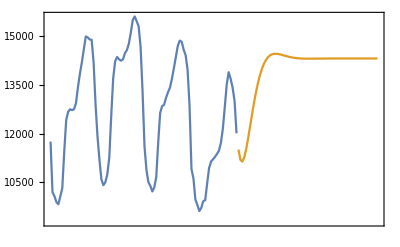

```mathematica
DateListPlot[{TimeSeriesWindow[loadtimeseriesResampled,{DateObject[{2019,6,5}],DateObject[{2019,8,24}]}],forecast}]
```

```mathematica
subtractedTS=Subtract[loadtimeseriesResampled,Min[loadtimeseriesResampled]]
```

TimeSeries[…]

```mathematica
Min[subtractedTS]
```

0.

```mathematica
subtractedloadmodelfit=TimeSeriesModelFit[subtractedTS]
```

TimeSeriesModel[…]

```mathematica
subtractedforecast=TimeSeriesForecast[subtractedloadmodelfit,{72}]
```

TemporalData[…]

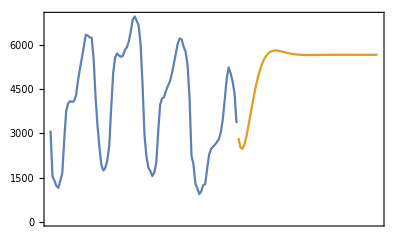

```mathematica
DateListPlot[{TimeSeriesWindow[subtractedTS,{DateObject[{2019,6,5}],DateObject[{2019,8,24}]}],subtractedforecast}]
```